```mathematica
(*This is the path that contains the executables and loads SDPB*)
executablesPath = "/home/pano/.local/src/sdpb/build";
<<"/home/pano/.local/src/sdpb/mathematica/SDPB.m";
```

# Gap Consistency Checks

## We constrain possible values for the Gap of a CFT by searching for a functional which breaks everything hehe.

## Defining the Matrix Problem

Let’s first construct the matrix problem and tell SDPB to export the description into a JSON file for SDPB to actually run the thing.

{-8.16814,-352.979,-4477.28,118740.,-3.20862×10^6,1.19923×10^8,-6.69562×10^9,5.38329×10^11,-5.58466×10^13,6.69963×10^15,-8.50605×10^17,1.03759×10^20,-9.81605×10^21,-1.14452×10^23}

terminateReason = "found primal-dual optimal solution";
primalObjective = -0.0641488199318168919664592177604502997214247333281800175451753773241639589861603;
dualObjective   = -0.06414881993181689197014465176897774967483199660616302064196741974352366845542625;
dualityGap      = 3.685434008527449953407263277983003096792042419359709469265950780108579896152853e-21;
primalError     = 6.411311360537038170035086067730061894167758990207137541462599330092505990358017e-36;
dualError       = 3.882711483448281272412136161644039771966095386698426656794531874664312564304249e-45;
Solver runtime  = 4;

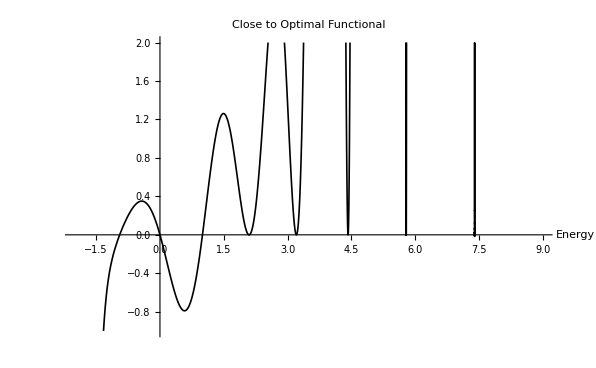

```mathematica
(*Precision and directories*)
precision = 1024;
file ="/home/pano/projects/sdpb-test/pmp.json";
sdpdir="/home/pano/projects/sdpb-test/sdp";
outdir="/home/pano/projects/sdpb-test/out";
outfile ="/home/pano/projects/sdpb-test/out/z.txt";
Run[StringRiffle[{
"rm -rf",
FileNameJoin[sdpdir,"*"],
sdpdir<>".ck",
FileNameJoin[outdir,"*"]
}]];

(*Maximum order of derivatives in the linear functional a*)
P=27; 

(*Central charge*)
c = 12; 

(*Gap energy*)
E0=1; 

(*Polynomial generator function*)
poly[n_,E0_,x_]:=Sum[StirlingS2[n,k](-2π (x+E0))^k,{k,1,n}]; 

(*Construct a module that does this whole sdpb definition thingy*)
solve[gapEnergy_:E0,centralCharge_:c, order_:P, precision_:prec]:=
Module[{
E0=gapEnergy,
c=centralCharge,
NN=Floor[order/2],
prec=precision,
objective,
normalization,
matrices
},

(*Objective vector*)
(*objective = {0}~Join~(poly[2#+1,0,-c/12]&/@Range[0,NN]);*)
objective = (poly[2#+1,0,-c/12]&/@Range[0,NN]);

(*Normalization vector*)
(*normalization = (Range[0,NN]*0);*)
normalization = (poly[2#+1,E0,0.3]&/@Range[0,NN]);
Echo[normalization];

(*Polynomial list*)
matrices={
PositiveMatrixWithPrefactor[<|
(*"polynomials"->{{{-x}~Join~(Expand[poly[2#+1,E0,x],x]&/@Range[0,NN])}}*)
"polynomials"->{{(Expand[poly[2#+1,E0,x],x]&/@Range[0,NN])}}
|>]
};

(*Define SDP*)
WritePmpJson[file, SDP[objective,normalization,matrices], prec];

(*Run the magical code to solve*)
Run[StringRiffle[{
FileNameJoin[{executablesPath,"pmp2sdp"}],
ToString[prec], file, sdpdir
}]];
Run[StringRiffle[{
"mpirun",
FileNameJoin[{executablesPath,"sdpb"}],
"-s", sdpdir, "-o", outdir,
"--precision", ToString[prec],
"--noFinalCheckpoint"
,"--maxIterations",ToString[1000]
,"--dualityGapThreshold 1e-20"
, "--writeSolution=\"x,y,z\""
}]];
(*ToExpression@Import[FileNameJoin[{outdir,"out.txt"}],"Text"];*)
fullResult = Import[FileNameJoin[{outdir,"out.txt"}], "String"]
];
solve[]
(* Get the optimal vector *)
α=(Import[outfile,"Table"][[2;;]]//Flatten).(poly[2#+1,0,x]&/@Range[0,Floor[P/2]])//Simplify;
Plot[α,{x,-c/12-E0,9},PlotRange->{-1,2} ,MaxRecursion->15,AxesLabel->{HoldForm[Energy],None},PlotLabel->HoldForm[Close to Optimal Functional],LabelStyle->{8},PlotStyle->{Black,Thickness[0.002]}]
```

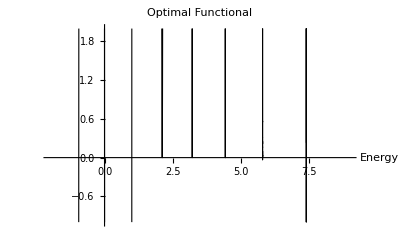

```mathematica
Plot[α,{x,-c/12-E0,9},PlotRange->{-1,2} ,MaxRecursion->15,AxesLabel->{HoldForm[Energy],None},PlotLabel->HoldForm[Optimal Functional],LabelStyle->{8},PlotStyle->{Black,Thickness[0.002]}]
```

```mathematica
(*StringRiffle[{
"rm -rf",
FileNameJoin[sdpdir,"*"],
sdpdir<>".ck",
FileNameJoin[outdir,"*"],
"&&",
FileNameJoin[{executablesPath,"pmp2sdp"}],
ToString[prec], file, sdpdir,
 "&&",
"mpirun",
FileNameJoin[{executablesPath,"sdpb"}],
"-s", sdpdir, "-o", outdir,
"--precision", ToString[prec],
"--noFinalCheckpoint"
,"--maxIterations",ToString[1000]
,"--dualityGapThreshold 1e-10"
, "--writeSolution=\"x,y,z\""
}]*)
```